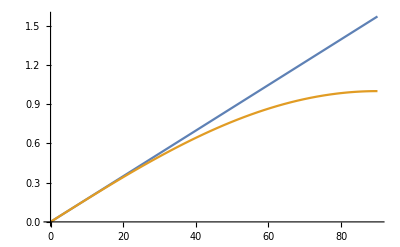

```mathematica
Plot[{x °,Sin[x °]},{x,0,90}] (*Comparacion del angulo con la funcion seno, muy similar a pequena escala*)
```

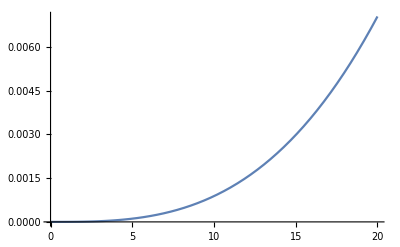

```mathematica
Plot[{x °-Sin[x °]},{x,0,20}] (*He aqui la diferencia, notece que en angulos pequenos es muy chica, entre mas crece la diferencia se hace significativa*)
```

```mathematica
Table[{x,x °-Sin[x °]},{x,0,25,1.}]//TableForm (*aqui listadas las diferencias en base a valores del angulo, de 0 a 25 grados*)
```

0. | 0.
1. | 8.86083×10^-7
2. | 7.08834×10^-6
3. | 0.0000239213
4. | 0.0000566963
5. | 0.00011072
6. | 0.000191292
7. | 0.000303704
8. | 0.000453239
9. | 0.000645168
10. | 0.000884748
11. | 0.00117722
12. | 0.00152782
13. | 0.00194175
14. | 0.0024242
15. | 0.00298034
16. | 0.00361532
17. | 0.00433427
18. | 0.00514227
19. | 0.0060444
20. | 0.00704571
21. | 0.00815119
22. | 0.00936584
23. | 0.0106946
24. | 0.0121424
25. | 0.0137141

```mathematica
(*MAS*)
ecd=θ''[t]+ω^2 θ[t]==0; (*he aqui la ecuacion de movimiento armonico, que nos dice como la aceleracion angular es igual a omega al cuadrado por el desplazamiento del angulo (esta expresion para angulos pequenos)*)
```

```mathematica
First[DSolve[ecd,θ,t]] (*Resolvemos la ecuacion diferencial*)
```

{θ→Function[{t},C[1] Cos[t ω]+C[2] Sin[t ω]]}

```mathematica
sol1[t_]=θ[t]/.First@DSolve[ecd,θ,t] (*hacemos una funcion para la solucion, aplicando la solucion simbolica de antes*)
```

C[1] Cos[t ω]+C[2] Sin[t ω]

```mathematica
Solve[{sol1[0]==θ0, sol1'[0]==θp0},{C[1],C[2]}] (*resolvemos por las constantes usando valores iniciales*)
```

{{C[1]→θ0,C[2]→θp0/ω}}

```mathematica
DSolve[{ecd,θ[0]==θ0,θ'[0]==θp0},θ,t] (*aqui resolvemos la ecuacion directamente con los valores iniciales, notece que llegamos a las mismas constantes*)
```

{{θ→Function[{t},(θ0 ω Cos[t ω]+θp0 Sin[t ω])/ω]}}

```mathematica
soln[t_]=θ[t]/.First@NDSolve[{ecd/.ω->1,θ[0]==15°,θ'[0]==0},θ[t],{t,0,10}]
```

InterpolatingFunction[…][t]

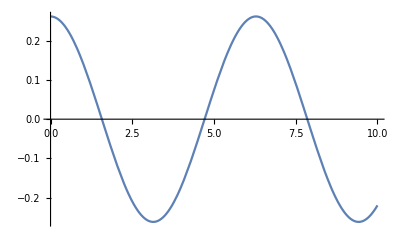

```mathematica
Plot[soln[t],{t,0,10}]
```

Plot del movimiento de un pendulo con largo variable “l”

```mathematica
Manipulate[Plot[θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==15°,θ'[0]==0},θ[t],{t,0,10}]/.t->T,{T,0,10}],{l,.1,10,.1}]
```

```mathematica
ecd2=θ''[t]+ω^2 Sin[θ[t]]==0; (*he aqui la ecuacion sin aproximacion del movimiento armonico simple*)
```

```mathematica
Manipulate[Plot[{(θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}]),(θ[t]/.First@NDSolve[{ecd2/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}])}/.t->T,{T,0,10}],{{l,1},.1,10,.1},{{angulo,15},1,45,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of ecd2 in the first argument {ecd2,θ[0]==45 °,θ'[0]==0}.

ReplaceAll::reps: {ecd2,θ[0]==45 °,θ'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ecd2,θ[0.]==0.785398,θ'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of ecd2 in the first argument {ecd2,θ[0]==45 °,θ'[0]==0}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{(θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}])-(θ[t]/.First@NDSolve[{ecd2/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}])}/.t->T,{T,0,10}],{{l,1},.1,10,.1},{{angulo,15},1,45,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of ecd2 in the first argument {ecd2,θ[0]==13 °,θ'[0]==0}.

ReplaceAll::reps: {ecd2,θ[0]==13 °,θ'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ecd2,θ[0.]==0.226893,θ'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of ecd2 in the first argument {ecd2,θ[0]==13 °,θ'[0]==0}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{(θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,tfin}]),(θ[t]/.First@NDSolve[{ecd2/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,tfin}])}/.t->T,{T,tfin-10,tfin}],{{l,1},.1,10,.1},{{angulo,15},1,45,1},{{tfin,80},10,100}]
```

NDSolve::deqn: Equation or list of equations expected instead of ecd2 in the first argument {ecd2,θ[0]==3 °,θ'[0]==0}.

ReplaceAll::reps: {ecd2,θ[0]==3 °,θ'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ecd2,θ[0.]==0.0523599,θ'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of ecd2 in the first argument {ecd2,θ[0]==3 °,θ'[0]==0}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

```mathematica
p[q_,r_,r1_]:=q/Norm[r-r1]
```

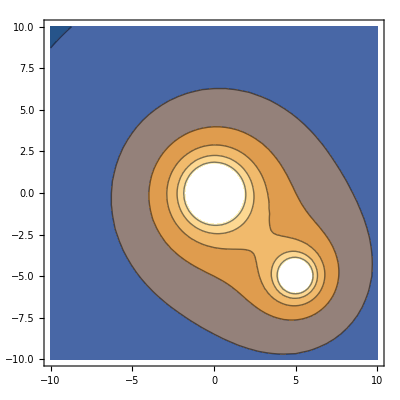

```mathematica
ContourPlot[p[10,{x,y},{0,0}]+p[5,{x,y},{5,-5}],{x,-10,10},{y,-10,10}]
```

```mathematica
Grad[p[10,{x,y},{0,0}],{x,y}]
```

{-(10 Abs[x] Abs'[x])/((Abs[x]^2+Abs[y]^2)^(3/2)),-(10 Abs[y] Abs'[y])/((Abs[x]^2+Abs[y]^2)^(3/2))}

```mathematica
e[q_,r_,r1_]:=q(r-r1)/Norm[r-r1]^3
```

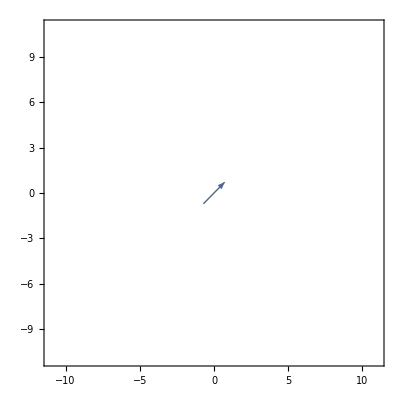

```mathematica
VectorPlot[e[10,{x,y},{0,0}],{x,-10,10},{y,-10,10}]
```

```mathematica
e[10,{2,2},{0,0}]
```

{5/(4 √2),5/(4 √2)}

```mathematica
VectorPlot[Grad[p[10,{x,y},{0,0}],{x,y}],{x,-10,10},{y,-10,10}]
```

-Graphics-